Analysis of hfi using Schrieffer-Wolff transformation with respect to electronic zero-field splitting

## electron + single n-spin

### Definitions

```mathematica
σ0=({{1, 0}, {0, 1}}); σx=({{0, 1}, {1, 0}}); σy=({{0, -I}, {I, 0}});σz=({{1, 0}, {0, -1}}); (* Pauli matrices *)
```

```mathematica
S0=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});Sx=1/(√2)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}});Sy=1/(√2)({{0, -I, 0}, {I, 0, -I}, {0, I, 0}});Sz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});    (* Spin 1 matrices *)
```

```mathematica
MF=MatrixForm
```

MatrixForm

```mathematica
(* Ij = Spin 1/2 !!! *)
Op2Mat[ham_]:=Flatten[Table[ham
/.{Subscript[S, x]-> (Sp+Sm)/2,Subscript[S, y]-> (Sp-Sm)/(2ⅈ),Subscript[Ij, x]-> (Ijp+Ijm)/2,Subscript[Ij, y]-> (Ijp-Ijm)/(2ⅈ)}
/.{Subscript[S, 0]->If[Subscript[Sl, z]==Subscript[Sr, z],1,0],
Subscript[S, z]->If[Subscript[Sl, z]==Subscript[Sr, z],Subscript[Sl, z],0],
Sp->If[Subscript[Sl, z]==Subscript[Sr, z]+1,√2,0],
Sm->If[Subscript[Sl, z]==Subscript[Sr, z]-1,√2,0],
Subscript[Ij, 0]->If[Subscript[Ijl, z]==Subscript[Ijr, z],1,0],
Subscript[Ij, z]->If[Subscript[Ijl, z]==Subscript[Ijr, z],Subscript[Ijl, z],0],
Ijp->If[Subscript[Ijl, z]==Subscript[Ijr, z]+1,1,0],
Ijm->If[Subscript[Ijl, z]==Subscript[Ijr, z]-1,1,0]}
,{Subscript[Sl, z],{+1,0,-1}},{Subscript[Ijl, z],{+1/2,-1/2}},{Subscript[Sr, z],{+1,0,-1}},{Subscript[Ijr, z],{+1/2,-1/2}}]
,{{1,2},{3,4}}];
```

### Most general, e.g. ^13C [Childress2006]

```mathematica
Bvec={Subscript[B, x],Subscript[B, y],Subscript[B, z]};
Ijvec={Subscript[Ij, x],Subscript[Ij, y],Subscript[Ij, z]};
```

```mathematica
H00=Δ Subscript[S, z]^2 Subscript[Ij, 0]-Subscript[μ, e] Subscript[B, z] Subscript[S, z] Subscript[Ij, 0];(*for energy denominators; zeroth order approximation*)
H0=Δ Subscript[S, z]^2 Subscript[Ij, 0]-Subscript[μ, e] Subscript[B, z] Subscript[S, z] Subscript[Ij, 0]-Subscript[S, 0] Subscript[μ, n] Bvec.Ijvec+Subscript[S, z](Subscript[α, zx] Subscript[Ij, x]+Subscript[α, zy] Subscript[Ij, y]+Subscript[α, zz] Subscript[Ij, z]);
U=-Subscript[μ, e](Subscript[B, x] Subscript[S, x]+Subscript[B, y] Subscript[S, y])Subscript[Ij, 0]+ϵ Subscript[S, x](Subscript[α, xx] Subscript[Ij, x]+Subscript[α, xy] Subscript[Ij, y]+Subscript[α, xz] Subscript[Ij, z])+ϵ Subscript[S, y](Subscript[α, yx] Subscript[Ij, x]+Subscript[α, yy] Subscript[Ij, y]+Subscript[α, yz] Subscript[Ij, z]);(* U = non-secular terms; 
ϵ is small parameter used for perturbative expansion in non-secular hfi components *)
```

```mathematica
H00MAT=Op2Mat[H00];
H0MAT=Op2Mat[H0];
UMAT=Op2Mat[U];
```

```mathematica
MatrixForm[H0MAT,TableDepth->2]
```

(Δ+α_zz/2-B_z μ_e-(B_z μ_n)/2 | α_zx/2-(ⅈ α_zy)/2-(B_x/2-(ⅈ B_y)/2) μ_n | 0 | 0 | 0 | 0
α_zx/2+(ⅈ α_zy)/2-(B_x/2+(ⅈ B_y)/2) μ_n | Δ-α_zz/2-B_z μ_e+(B_z μ_n)/2 | 0 | 0 | 0 | 0
0 | 0 | -1/2 B_z μ_n | -(B_x/2-(ⅈ B_y)/2) μ_n | 0 | 0
0 | 0 | -(B_x/2+(ⅈ B_y)/2) μ_n | (B_z μ_n)/2 | 0 | 0
0 | 0 | 0 | 0 | Δ-α_zz/2+B_z μ_e-(B_z μ_n)/2 | -α_zx/2+(ⅈ α_zy)/2-(B_x/2-(ⅈ B_y)/2) μ_n
0 | 0 | 0 | 0 | -α_zx/2-(ⅈ α_zy)/2-(B_x/2+(ⅈ B_y)/2) μ_n | Δ+α_zz/2+B_z μ_e+(B_z μ_n)/2)

```mathematica
MatrixForm[UMAT/.ϵ->1,TableDepth->2]
```

(0 | 0 | α_xz/(2 √2)-(ⅈ α_yz)/(2 √2)-(B_x/(√2)-(ⅈ B_y)/(√2)) μ_e | (α_xx/2-(ⅈ α_xy)/2)/(√2)-(ⅈ (α_yx/2-(ⅈ α_yy)/2))/(√2) | 0 | 0
0 | 0 | (α_xx/2+(ⅈ α_xy)/2)/(√2)-(ⅈ (α_yx/2+(ⅈ α_yy)/2))/(√2) | -α_xz/(2 √2)+(ⅈ α_yz)/(2 √2)-(B_x/(√2)-(ⅈ B_y)/(√2)) μ_e | 0 | 0
α_xz/(2 √2)+(ⅈ α_yz)/(2 √2)-(B_x/(√2)+(ⅈ B_y)/(√2)) μ_e | (α_xx/2-(ⅈ α_xy)/2)/(√2)+(ⅈ (α_yx/2-(ⅈ α_yy)/2))/(√2) | 0 | 0 | α_xz/(2 √2)-(ⅈ α_yz)/(2 √2)-(B_x/(√2)-(ⅈ B_y)/(√2)) μ_e | (α_xx/2-(ⅈ α_xy)/2)/(√2)-(ⅈ (α_yx/2-(ⅈ α_yy)/2))/(√2)
(α_xx/2+(ⅈ α_xy)/2)/(√2)+(ⅈ (α_yx/2+(ⅈ α_yy)/2))/(√2) | -α_xz/(2 √2)-(ⅈ α_yz)/(2 √2)-(B_x/(√2)+(ⅈ B_y)/(√2)) μ_e | 0 | 0 | (α_xx/2+(ⅈ α_xy)/2)/(√2)-(ⅈ (α_yx/2+(ⅈ α_yy)/2))/(√2) | -α_xz/(2 √2)+(ⅈ α_yz)/(2 √2)-(B_x/(√2)-(ⅈ B_y)/(√2)) μ_e
0 | 0 | α_xz/(2 √2)+(ⅈ α_yz)/(2 √2)-(B_x/(√2)+(ⅈ B_y)/(√2)) μ_e | (α_xx/2-(ⅈ α_xy)/2)/(√2)+(ⅈ (α_yx/2-(ⅈ α_yy)/2))/(√2) | 0 | 0
0 | 0 | (α_xx/2+(ⅈ α_xy)/2)/(√2)+(ⅈ (α_yx/2+(ⅈ α_yy)/2))/(√2) | -α_xz/(2 √2)-(ⅈ α_yz)/(2 √2)-(B_x/(√2)+(ⅈ B_y)/(√2)) μ_e | 0 | 0)

```mathematica
blocks={{1,2},{3,4},{5,6}};
nb=Length[Flatten[blocks]];
NB=Length[blocks];
LöMAT=Table[0,{m,nb},{mp,nb}];
```

```mathematica
LöMAT=Table[0,{i,NB},{j,NB}];
Do[LöMAT[[i,i]]=Take[H0MAT,blocks[[i]],blocks[[i]]],{i,NB}];
LöMAT=ArrayFlatten[LöMAT];
```

```mathematica
Do[Do[LöMAT[[m,mp]]=LöMAT[[m,mp]]+1/2 Sum[UMAT[[m,l]]UMAT[[l,mp]](1/(H00MAT[[m,m]]-H00MAT[[l,l]])+1/(H00MAT[[mp,mp]]-H00MAT[[l,l]])),{l,Flatten[Delete[blocks,i]]}],{m,blocks[[i]]},{mp,blocks[[i]]}],
{i,NB}]
```

```mathematica
LöMAT=Simplify[LöMAT/.{Subscript[α, yx]->Subscript[α, xy],Subscript[α, yz]->Subscript[α, zy],Subscript[α, xz]->Subscript[α, zx]}];
```

```mathematica
Do[Print[Take[LöMAT,blocks[[i]],blocks[[i]]]//MF],{i,NB}]
```

((8 Δ^2+ϵ^2 α_xx^2+4 ϵ^2 α_xy^2-2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2+4 Δ α_zz-16 Δ B_z μ_e-4 ϵ B_x α_zx μ_e-4 ϵ B_y α_zy μ_e-4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2-4 Δ B_z μ_n+4 B_z^2 μ_e μ_n)/(8 Δ-8 B_z μ_e) | (-ⅈ α_zy (2 Δ+ϵ^2 α_xx-ⅈ ϵ^2 α_xy-2 B_z μ_e)+α_zx (2 Δ+ⅈ ϵ^2 α_xy+ϵ^2 α_yy-2 B_z μ_e)-2 (B_x (ϵ α_xx μ_e-ⅈ ϵ α_xy μ_e+(Δ-B_z μ_e) μ_n)-ⅈ B_y (ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ-B_z μ_e) μ_n)))/(4 (Δ-B_z μ_e))
(α_zx (2 Δ-ⅈ ϵ^2 α_xy+ϵ^2 α_yy-2 B_z μ_e)+ⅈ (α_zy (2 Δ+ϵ^2 α_xx+ⅈ ϵ^2 α_xy-2 B_z μ_e)+2 ⅈ (B_x (ϵ α_xx μ_e+ⅈ ϵ α_xy μ_e+(Δ-B_z μ_e) μ_n)+B_y (ϵ α_xy μ_e+ⅈ (ϵ α_yy μ_e+(Δ-B_z μ_e) μ_n)))))/(4 (Δ-B_z μ_e)) | (8 Δ^2+ϵ^2 α_xx^2+2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2-4 Δ α_zz-16 Δ B_z μ_e+4 ϵ B_x α_zx μ_e+4 ϵ B_y α_zy μ_e+4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2+4 Δ B_z μ_n-4 B_z^2 μ_e μ_n)/(8 Δ-8 B_z μ_e))

(-(Δ ϵ^2 α_xx^2+Δ ϵ^2 α_yy^2+Δ ϵ^2 α_zx^2+Δ ϵ^2 α_zy^2+2 ϵ^2 B_z α_xx α_yy μ_e-4 Δ ϵ B_x α_zx μ_e-4 Δ ϵ B_y α_zy μ_e+4 Δ B_x^2 μ_e^2+4 Δ B_y^2 μ_e^2+2 ϵ^2 α_xy^2 (Δ-B_z μ_e)+2 Δ^2 B_z μ_n-2 B_z^3 μ_e^2 μ_n)/(4 (Δ^2-B_z^2 μ_e^2)) | (ϵ^2 B_z (α_yy α_zx+ⅈ α_xy (α_zx+ⅈ α_zy)-ⅈ α_xx α_zy) μ_e+B_x (2 Δ ϵ α_xx μ_e-2 ⅈ Δ ϵ α_xy μ_e+(-Δ^2+B_z^2 μ_e^2) μ_n)+B_y (2 Δ ϵ α_xy μ_e+ⅈ (-2 Δ ϵ α_yy μ_e+(Δ^2-B_z^2 μ_e^2) μ_n)))/(2 (Δ^2-B_z^2 μ_e^2))
(ϵ^2 B_z (α_yy α_zx+α_xy (-ⅈ α_zx-α_zy)+ⅈ α_xx α_zy) μ_e+B_x (2 Δ ϵ α_xx μ_e+2 ⅈ Δ ϵ α_xy μ_e+(-Δ^2+B_z^2 μ_e^2) μ_n)+B_y (2 Δ ϵ α_xy μ_e-ⅈ (-2 Δ ϵ α_yy μ_e+(Δ^2-B_z^2 μ_e^2) μ_n)))/(2 (Δ^2-B_z^2 μ_e^2)) | -(Δ ϵ^2 α_xx^2+Δ ϵ^2 α_yy^2+Δ ϵ^2 α_zx^2+Δ ϵ^2 α_zy^2-2 ϵ^2 B_z α_xx α_yy μ_e+4 Δ ϵ B_x α_zx μ_e+4 Δ ϵ B_y α_zy μ_e+4 Δ B_x^2 μ_e^2+4 Δ B_y^2 μ_e^2+2 ϵ^2 α_xy^2 (Δ+B_z μ_e)-2 Δ^2 B_z μ_n+2 B_z^3 μ_e^2 μ_n)/(4 (Δ^2-B_z^2 μ_e^2)))

((8 Δ^2+ϵ^2 α_xx^2+2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2-4 Δ α_zz+16 Δ B_z μ_e-4 ϵ B_x α_zx μ_e-4 ϵ B_y α_zy μ_e-4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2-4 Δ B_z μ_n-4 B_z^2 μ_e μ_n)/(8 Δ+8 B_z μ_e) | (-α_zx (ⅈ ϵ^2 α_xy+ϵ^2 α_yy+2 (Δ+B_z μ_e))+ⅈ (α_zy (ϵ^2 α_xx-ⅈ ϵ^2 α_xy+2 (Δ+B_z μ_e))+2 (ⅈ B_x (ϵ α_xx μ_e-ⅈ ϵ α_xy μ_e+(Δ+B_z μ_e) μ_n)+B_y (ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ+B_z μ_e) μ_n))))/(4 (Δ+B_z μ_e))
-(ⅈ α_zy (ϵ^2 α_xx+ⅈ ϵ^2 α_xy+2 (Δ+B_z μ_e))+α_zx (-ⅈ ϵ^2 α_xy+ϵ^2 α_yy+2 (Δ+B_z μ_e))+2 (B_x (ϵ α_xx μ_e+ⅈ ϵ α_xy μ_e+(Δ+B_z μ_e) μ_n)+ⅈ B_y (-ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ+B_z μ_e) μ_n)))/(4 (Δ+B_z μ_e)) | (8 Δ^2+ϵ^2 α_xx^2+4 ϵ^2 α_xy^2-2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2+4 Δ α_zz+16 Δ B_z μ_e+4 ϵ B_x α_zx μ_e+4 ϵ B_y α_zy μ_e+4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2+4 Δ B_z μ_n+4 B_z^2 μ_e μ_n)/(8 Δ+8 B_z μ_e))

```mathematica
Do[Print[Take[LöMAT,blocks[[i]],blocks[[i]]]//MF],{i,NB}]
```

((8 Δ^2+ϵ^2 α_xx^2+4 ϵ^2 α_xy^2-2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2+4 Δ α_zz-16 Δ B_z μ_e-4 ϵ B_x α_zx μ_e-4 ϵ B_y α_zy μ_e-4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2-4 Δ B_z μ_n+4 B_z^2 μ_e μ_n)/(8 Δ-8 B_z μ_e) | (-ⅈ α_zy (2 Δ+ϵ^2 α_xx-ⅈ ϵ^2 α_xy-2 B_z μ_e)+α_zx (2 Δ+ⅈ ϵ^2 α_xy+ϵ^2 α_yy-2 B_z μ_e)-2 (B_x (ϵ α_xx μ_e-ⅈ ϵ α_xy μ_e+(Δ-B_z μ_e) μ_n)-ⅈ B_y (ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ-B_z μ_e) μ_n)))/(4 (Δ-B_z μ_e))
(α_zx (2 Δ-ⅈ ϵ^2 α_xy+ϵ^2 α_yy-2 B_z μ_e)+ⅈ (α_zy (2 Δ+ϵ^2 α_xx+ⅈ ϵ^2 α_xy-2 B_z μ_e)+2 ⅈ (B_x (ϵ α_xx μ_e+ⅈ ϵ α_xy μ_e+(Δ-B_z μ_e) μ_n)+B_y (ϵ α_xy μ_e+ⅈ (ϵ α_yy μ_e+(Δ-B_z μ_e) μ_n)))))/(4 (Δ-B_z μ_e)) | (8 Δ^2+ϵ^2 α_xx^2+2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2-4 Δ α_zz-16 Δ B_z μ_e+4 ϵ B_x α_zx μ_e+4 ϵ B_y α_zy μ_e+4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2+4 Δ B_z μ_n-4 B_z^2 μ_e μ_n)/(8 Δ-8 B_z μ_e))

(-(Δ ϵ^2 α_xx^2+Δ ϵ^2 α_yy^2+Δ ϵ^2 α_zx^2+Δ ϵ^2 α_zy^2+2 ϵ^2 B_z α_xx α_yy μ_e-4 Δ ϵ B_x α_zx μ_e-4 Δ ϵ B_y α_zy μ_e+4 Δ B_x^2 μ_e^2+4 Δ B_y^2 μ_e^2+2 ϵ^2 α_xy^2 (Δ-B_z μ_e)+2 Δ^2 B_z μ_n-2 B_z^3 μ_e^2 μ_n)/(4 (Δ^2-B_z^2 μ_e^2)) | (ϵ^2 B_z (α_yy α_zx+ⅈ α_xy (α_zx+ⅈ α_zy)-ⅈ α_xx α_zy) μ_e+B_x (2 Δ ϵ α_xx μ_e-2 ⅈ Δ ϵ α_xy μ_e+(-Δ^2+B_z^2 μ_e^2) μ_n)+B_y (2 Δ ϵ α_xy μ_e+ⅈ (-2 Δ ϵ α_yy μ_e+(Δ^2-B_z^2 μ_e^2) μ_n)))/(2 (Δ^2-B_z^2 μ_e^2))
(ϵ^2 B_z (α_yy α_zx+α_xy (-ⅈ α_zx-α_zy)+ⅈ α_xx α_zy) μ_e+B_x (2 Δ ϵ α_xx μ_e+2 ⅈ Δ ϵ α_xy μ_e+(-Δ^2+B_z^2 μ_e^2) μ_n)+B_y (2 Δ ϵ α_xy μ_e-ⅈ (-2 Δ ϵ α_yy μ_e+(Δ^2-B_z^2 μ_e^2) μ_n)))/(2 (Δ^2-B_z^2 μ_e^2)) | -(Δ ϵ^2 α_xx^2+Δ ϵ^2 α_yy^2+Δ ϵ^2 α_zx^2+Δ ϵ^2 α_zy^2-2 ϵ^2 B_z α_xx α_yy μ_e+4 Δ ϵ B_x α_zx μ_e+4 Δ ϵ B_y α_zy μ_e+4 Δ B_x^2 μ_e^2+4 Δ B_y^2 μ_e^2+2 ϵ^2 α_xy^2 (Δ+B_z μ_e)-2 Δ^2 B_z μ_n+2 B_z^3 μ_e^2 μ_n)/(4 (Δ^2-B_z^2 μ_e^2)))

((8 Δ^2+ϵ^2 α_xx^2+2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2-4 Δ α_zz+16 Δ B_z μ_e-4 ϵ B_x α_zx μ_e-4 ϵ B_y α_zy μ_e-4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2-4 Δ B_z μ_n-4 B_z^2 μ_e μ_n)/(8 Δ+8 B_z μ_e) | (-α_zx (ⅈ ϵ^2 α_xy+ϵ^2 α_yy+2 (Δ+B_z μ_e))+ⅈ (α_zy (ϵ^2 α_xx-ⅈ ϵ^2 α_xy+2 (Δ+B_z μ_e))+2 (ⅈ B_x (ϵ α_xx μ_e-ⅈ ϵ α_xy μ_e+(Δ+B_z μ_e) μ_n)+B_y (ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ+B_z μ_e) μ_n))))/(4 (Δ+B_z μ_e))
-(ⅈ α_zy (ϵ^2 α_xx+ⅈ ϵ^2 α_xy+2 (Δ+B_z μ_e))+α_zx (-ⅈ ϵ^2 α_xy+ϵ^2 α_yy+2 (Δ+B_z μ_e))+2 (B_x (ϵ α_xx μ_e+ⅈ ϵ α_xy μ_e+(Δ+B_z μ_e) μ_n)+ⅈ B_y (-ⅈ ϵ α_xy μ_e+ϵ α_yy μ_e+(Δ+B_z μ_e) μ_n)))/(4 (Δ+B_z μ_e)) | (8 Δ^2+ϵ^2 α_xx^2+4 ϵ^2 α_xy^2-2 ϵ^2 α_xx α_yy+ϵ^2 α_yy^2+ϵ^2 α_zx^2+ϵ^2 α_zy^2+4 Δ α_zz+16 Δ B_z μ_e+4 ϵ B_x α_zx μ_e+4 ϵ B_y α_zy μ_e+4 B_z α_zz μ_e+4 B_x^2 μ_e^2+4 B_y^2 μ_e^2+8 B_z^2 μ_e^2+4 Δ B_z μ_n+4 B_z^2 μ_e μ_n)/(8 Δ+8 B_z μ_e))

remove higher than linear order in α terms

```mathematica
bh=Table[0,{i,NB}];
Do[
bh[[i]]=Simplify[Normal[Series[Take[LöMAT,blocks[[i]],blocks[[i]]],{ϵ,0,1}]]/.ϵ->1];
Print[bh[[i]]//MF],
{i,NB}]
```

((2 Δ^2-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2+α_zz (Δ-B_z μ_e)+B_z^2 μ_e (2 μ_e+μ_n)-Δ B_z (4 μ_e+μ_n))/(2 (Δ-B_z μ_e)) | 1/2 (α_zx-ⅈ α_zy+((B_x (α_xx-ⅈ α_xy)+B_y (α_xy-ⅈ α_yy)) μ_e)/(-Δ+B_z μ_e)-(B_x-ⅈ B_y) μ_n)
1/2 (α_zx+((B_x (α_xx+ⅈ α_xy)+B_y (α_xy+ⅈ α_yy)) μ_e)/(-Δ+B_z μ_e)+ⅈ (α_zy+ⅈ (B_x+ⅈ B_y) μ_n)) | (2 Δ^2+B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2+α_zz (-Δ+B_z μ_e)+B_z^2 μ_e (2 μ_e-μ_n)+Δ B_z (-4 μ_e+μ_n))/(2 (Δ-B_z μ_e)))

((2 Δ B_x α_zx μ_e+2 Δ B_y α_zy μ_e-2 Δ B_x^2 μ_e^2-2 Δ B_y^2 μ_e^2-Δ^2 B_z μ_n+B_z^3 μ_e^2 μ_n)/(2 Δ^2-2 B_z^2 μ_e^2) | (Δ (B_x (α_xx-ⅈ α_xy)+B_y (α_xy-ⅈ α_yy)) μ_e)/(Δ^2-B_z^2 μ_e^2)-1/2 (B_x-ⅈ B_y) μ_n
(Δ (B_x (α_xx+ⅈ α_xy)+B_y (α_xy+ⅈ α_yy)) μ_e)/(Δ^2-B_z^2 μ_e^2)-1/2 (B_x+ⅈ B_y) μ_n | -(2 Δ B_x α_zx μ_e+2 Δ B_y α_zy μ_e+2 Δ B_x^2 μ_e^2+2 Δ B_y^2 μ_e^2+B_z (-Δ^2+B_z^2 μ_e^2) μ_n)/(2 (Δ^2-B_z^2 μ_e^2)))

((2 Δ^2-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2-α_zz (Δ+B_z μ_e)+B_z^2 μ_e (2 μ_e-μ_n)+Δ B_z (4 μ_e-μ_n))/(2 (Δ+B_z μ_e)) | 1/4 (-(2 (B_x (α_xx-ⅈ α_xy)+B_y (α_xy-ⅈ α_yy)) μ_e)/(Δ+B_z μ_e)-2 (α_zx-ⅈ (α_zy+(ⅈ B_x+B_y) μ_n)))
1/4 (-(2 (B_x (α_xx+ⅈ α_xy)+B_y (α_xy+ⅈ α_yy)) μ_e)/(Δ+B_z μ_e)-2 (α_zx+ⅈ α_zy+(B_x+ⅈ B_y) μ_n)) | (2 Δ^2+B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2+α_zz (Δ+B_z μ_e)+B_z^2 μ_e (2 μ_e+μ_n)+Δ B_z (4 μ_e+μ_n))/(2 (Δ+B_z μ_e)))

```mathematica
Normal[Series[bh/.Δ->(1/invΔ),{invΔ,0,1}]]
```

{{{1/invΔ+1/2 invΔ (-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)+1/2 (α_zz-2 B_z μ_e-B_z μ_n),1/2 invΔ (-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)+1/2 (α_zx-ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)},{1/2 invΔ (-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)+1/2 (α_zx+ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n),1/invΔ+1/2 invΔ (B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)+1/2 (-α_zz-2 B_z μ_e+B_z μ_n)}},{{invΔ (B_x α_zx μ_e+B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)-(B_z μ_n)/2,invΔ (B_x α_xx μ_e-ⅈ B_x α_xy μ_e+B_y α_xy μ_e-ⅈ B_y α_yy μ_e)-(B_x μ_n)/2+1/2 ⅈ B_y μ_n},{invΔ (B_x α_xx μ_e+ⅈ B_x α_xy μ_e+B_y α_xy μ_e+ⅈ B_y α_yy μ_e)-(B_x μ_n)/2-1/2 ⅈ B_y μ_n,invΔ (-B_x α_zx μ_e-B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)+(B_z μ_n)/2}},{{1/invΔ-α_zz/2+B_z μ_e+1/2 invΔ (-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)-(B_z μ_n)/2,1/2 invΔ (-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)+1/2 (-α_zx+ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)},{1/2 invΔ (-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)+1/2 (-α_zx-ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n),1/invΔ+1/2 invΔ (B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)+1/2 (α_zz+2 B_z μ_e+B_z μ_n)}}}

```mathematica
bh=Normal[Series[bh/.Δ->(1/invΔ),{invΔ,0,1}]]/.invΔ->1/Δ
```

{{{Δ+(-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (α_zz-2 B_z μ_e-B_z μ_n),(-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (α_zx-ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)},{(-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (α_zx+ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n),Δ+(B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (-α_zz-2 B_z μ_e+B_z μ_n)}},{{(B_x α_zx μ_e+B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)/Δ-(B_z μ_n)/2,(B_x α_xx μ_e-ⅈ B_x α_xy μ_e+B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/Δ-(B_x μ_n)/2+1/2 ⅈ B_y μ_n},{(B_x α_xx μ_e+ⅈ B_x α_xy μ_e+B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/Δ-(B_x μ_n)/2-1/2 ⅈ B_y μ_n,(-B_x α_zx μ_e-B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)/Δ+(B_z μ_n)/2}},{{Δ-α_zz/2+B_z μ_e+(-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)-(B_z μ_n)/2,(-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (-α_zx+ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)},{(-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (-α_zx-ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n),Δ+(B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (α_zz+2 B_z μ_e+B_z μ_n)}}}

```mathematica
heff=Table[{Subscript[Heff, x], Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0]},{i,NB}];
Do[
heff[[i]]=heff[[i]]/.Solve[bh[[i]]==Subscript[Heff, 0] σ0+Subscript[Heff, z] σz/2+Subscript[Heff, x] σx/2+ Subscript[Heff, y] σy/2,{Subscript[Heff, x],Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0]}][[1]]
,{i,NB}];
Simplify[heff,Δ>0]//MF
```

((Δ α_zx-B_y α_xy μ_e-B_x (α_xx μ_e+Δ μ_n))/Δ | (Δ α_zy-B_x α_xy μ_e-B_y (α_yy μ_e+Δ μ_n))/Δ | -(-Δ α_zz+B_x α_zx μ_e+B_y α_zy μ_e+Δ B_z μ_n)/Δ | (2 Δ^2-2 Δ B_z μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)
(2 B_y α_xy μ_e+B_x (2 α_xx μ_e-Δ μ_n))/Δ | (2 B_x α_xy μ_e+B_y (2 α_yy μ_e-Δ μ_n))/Δ | (2 B_x α_zx μ_e+2 B_y α_zy μ_e-Δ B_z μ_n)/Δ | -((B_x^2+B_y^2) μ_e^2)/Δ
-(Δ α_zx+B_y α_xy μ_e+B_x (α_xx μ_e+Δ μ_n))/Δ | -(Δ α_zy+B_x α_xy μ_e+B_y (α_yy μ_e+Δ μ_n))/Δ | -(Δ α_zz+B_x α_zx μ_e+B_y α_zy μ_e+Δ B_z μ_n)/Δ | (2 Δ^2+2 Δ B_z μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ))

```mathematica
Simplify[heff/.{Subscript[B, x]^2->0,Subscript[B, y]^2->0},Δ>0]//MF
```

((Δ α_zx-B_y α_xy μ_e-B_x (α_xx μ_e+Δ μ_n))/Δ | (Δ α_zy-B_x α_xy μ_e-B_y (α_yy μ_e+Δ μ_n))/Δ | -(-Δ α_zz+B_x α_zx μ_e+B_y α_zy μ_e+Δ B_z μ_n)/Δ | Δ-B_z μ_e
(2 B_y α_xy μ_e+B_x (2 α_xx μ_e-Δ μ_n))/Δ | (2 B_x α_xy μ_e+B_y (2 α_yy μ_e-Δ μ_n))/Δ | (2 B_x α_zx μ_e+2 B_y α_zy μ_e-Δ B_z μ_n)/Δ | 0
-(Δ α_zx+B_y α_xy μ_e+B_x (α_xx μ_e+Δ μ_n))/Δ | -(Δ α_zy+B_x α_xy μ_e+B_y (α_yy μ_e+Δ μ_n))/Δ | -(Δ α_zz+B_x α_zx μ_e+B_y α_zy μ_e+Δ B_z μ_n)/Δ | Δ+B_z μ_e)

```mathematica
Simplify[heff/.{Subscript[B, x]->0,Subscript[B, y]->0},Δ>0]//MF
```

(α_zx | α_zy | α_zz-B_z μ_n | Δ-B_z μ_e
0 | 0 | -B_z μ_n | 0
-α_zx | -α_zy | -α_zz-B_z μ_n | Δ+B_z μ_e)

•  The B=0 term: 
S_z(α_zx Ij_x+α_zy Ij_y+α_zz Ij_z)

```mathematica
(heff/.{Subscript[B, x]->0,Subscript[B, y]->0,Subscript[B, z]->0}//MF)
```

(α_zx | α_zy | α_zz | Δ
0 | 0 | 0 | 0
-α_zx | -α_zy | -α_zz | Δ)

•  Effective g-tensor:

```mathematica
geff=Table[0,{i,NB},{j,3}];
Do[
geff[[i,j]]=D[heff[[i,1;;3]],Bvec[[j]]]
,{i,NB},{j,3}];
Do[Print["-μ_ng(m_s=",Sz[[i,i]],")=-μ_n𝕀_3+",Simplify[geff[[i]]+Subscript[μ, n] IdentityMatrix[3],Δ>0]//MF],{i,NB}]
```

-μ_ng(m_s=1)=-μ_n𝕀_3+(-(α_xx μ_e)/Δ | -(α_xy μ_e)/Δ | -(α_zx μ_e)/Δ
-(α_xy μ_e)/Δ | -(α_yy μ_e)/Δ | -(α_zy μ_e)/Δ
0 | 0 | 0)

-μ_ng(m_s=0)=-μ_n𝕀_3+((2 α_xx μ_e)/Δ | (2 α_xy μ_e)/Δ | (2 α_zx μ_e)/Δ
(2 α_xy μ_e)/Δ | (2 α_yy μ_e)/Δ | (2 α_zy μ_e)/Δ
0 | 0 | 0)

-μ_ng(m_s=-1)=-μ_n𝕀_3+(-(α_xx μ_e)/Δ | -(α_xy μ_e)/Δ | -(α_zx μ_e)/Δ
-(α_xy μ_e)/Δ | -(α_yy μ_e)/Δ | -(α_zy μ_e)/Δ
0 | 0 | 0)

•  combined

g^eff(m_s)=𝕀_3-(2-3|m_s|)(α_xx μ_e)/(μ_n Δ)(α_xx | α_xy | α_xz
α_xy | α_yy | α_yz
0 | 0 | 0)

•  This agrees with Childress et al.:   modified ^13C precession  ω^eff= μ_n B · g^eff
•  for B||z, the non-secular hfi components drop out in this approximation

#### Plot energy levels for magnetic field || z-axis

parameters for ^13C ,  hf parameter values are just examples

```mathematica
parameters={Δ->2.87 10^9,Subscript[μ, e]->28.031 10^9,Q->0,Subscript[μ, n]->10.705 10^6,Subscript[A, para]->5.0 10^3,Subscript[A, perp]->4.0 10^3};
```

```mathematica
Table[bh[[i]]//MF,{i,NB}]
```

{(Δ+(-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (α_zz-2 B_z μ_e-B_z μ_n) | (-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (α_zx-ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)
(-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (α_zx+ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n) | Δ+(B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (-α_zz-2 B_z μ_e+B_z μ_n)),((B_x α_zx μ_e+B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)/Δ-(B_z μ_n)/2 | (B_x α_xx μ_e-ⅈ B_x α_xy μ_e+B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/Δ-(B_x μ_n)/2+1/2 ⅈ B_y μ_n
(B_x α_xx μ_e+ⅈ B_x α_xy μ_e+B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/Δ-(B_x μ_n)/2-1/2 ⅈ B_y μ_n | (-B_x α_zx μ_e-B_y α_zy μ_e-B_x^2 μ_e^2-B_y^2 μ_e^2)/Δ+(B_z μ_n)/2),(Δ-α_zz/2+B_z μ_e+(-B_x α_zx μ_e-B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)-(B_z μ_n)/2 | (-B_x α_xx μ_e+ⅈ B_x α_xy μ_e-B_y α_xy μ_e+ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (-α_zx+ⅈ α_zy-B_x μ_n+ⅈ B_y μ_n)
(-B_x α_xx μ_e-ⅈ B_x α_xy μ_e-B_y α_xy μ_e-ⅈ B_y α_yy μ_e)/(2 Δ)+1/2 (-α_zx-ⅈ α_zy-B_x μ_n-ⅈ B_y μ_n) | Δ+(B_x α_zx μ_e+B_y α_zy μ_e+B_x^2 μ_e^2+B_y^2 μ_e^2)/(2 Δ)+1/2 (α_zz+2 B_z μ_e+B_z μ_n))}

```mathematica
Table[bh[[i]]/.{Subscript[B, x]->0,Subscript[B, y]->0}//MF,{i,NB}]
```

{(Δ+1/2 (α_zz-2 B_z μ_e-B_z μ_n) | 1/2 (α_zx-ⅈ α_zy)
1/2 (α_zx+ⅈ α_zy) | Δ+1/2 (-α_zz-2 B_z μ_e+B_z μ_n)),(-1/2 B_z μ_n | 0
0 | (B_z μ_n)/2),(Δ-α_zz/2+B_z μ_e-(B_z μ_n)/2 | 1/2 (-α_zx+ⅈ α_zy)
1/2 (-α_zx-ⅈ α_zy) | Δ+1/2 (α_zz+2 B_z μ_e+B_z μ_n))}

```mathematica
evals=Table[Eigenvalues[bh[[i]]/.{Subscript[B, x]->0,Subscript[B, y]->0}/.{Subscript[α, zz]->Subscript[A, para]}]/.{Subscript[α, zx]^2+Subscript[α, zy]^2->Subscript[A, perp]^2},{i,NB}]
```

{{1/2 (2 Δ-2 B_z μ_e-√(A_para^2+A_perp^2-2 A_para B_z μ_n+B_z^2 μ_n^2)),1/2 (2 Δ-2 B_z μ_e+√(A_para^2+A_perp^2-2 A_para B_z μ_n+B_z^2 μ_n^2))},{-1/2 B_z μ_n,(B_z μ_n)/2},{1/2 (2 Δ+2 B_z μ_e-√(A_para^2+A_perp^2+2 A_para B_z μ_n+B_z^2 μ_n^2)),1/2 (2 Δ+2 B_z μ_e+√(A_para^2+A_perp^2+2 A_para B_z μ_n+B_z^2 μ_n^2))}}

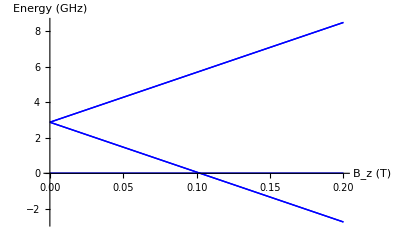

```mathematica
Plot[Evaluate[Table[evals[[i,m]]/10^9/.parameters,{i,NB},{m,1,2}]],{Subscript[B, z],0,0.2},￿￿AxesLabel->{"B_z (T)","Energy (GHz)"},PlotStyle->{{Thick,Blue}}]
```

on this ↑ scale one doesn't see nuclear spin effects, so remove electron Zeeman splitting   → nuclear Zeeman splitting visible:

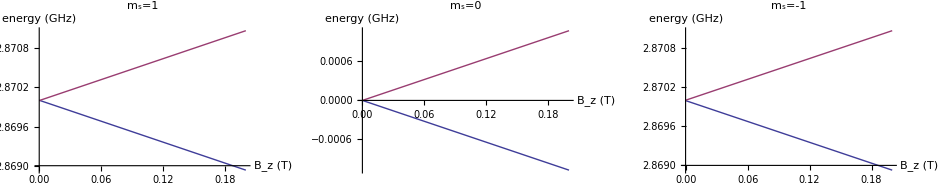

```mathematica
evalsnoZ=evals/.{Subscript[μ, e]->0};
{Table[Plot[Evaluate[Table[evalsnoZ[[i,m]]/10^9/.parameters,{m,1,2}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","energy (GHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]}//GraphicsGrid
```

remove zero-field splitting in plot

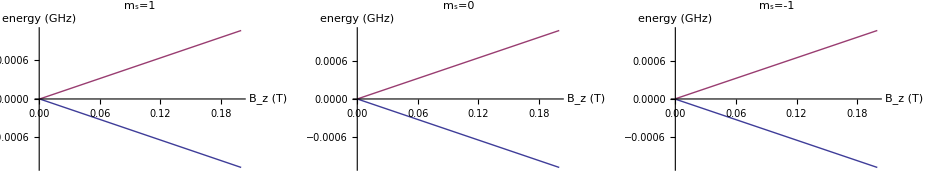

```mathematica
evalsnoZ=evals/.{Subscript[μ, e]->0};
{Table[Plot[Evaluate[Table[(evalsnoZ[[i,m]]-Δ Sz[[i,i]]^2)/10^9/.parameters,{m,1,2}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","energy (GHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]}//GraphicsGrid
```

zoom to see hyperfine shifts / avoided crossings (for m_s=+1 or m_s=-1 only)

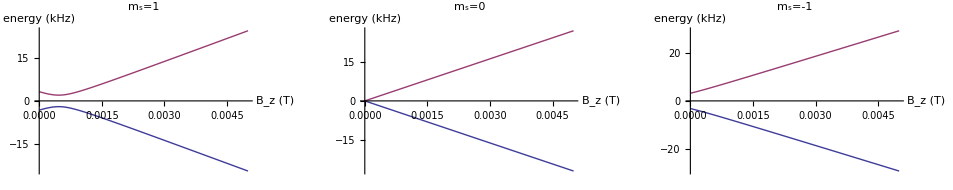

```mathematica
evalsnoZ=evals/.{Subscript[μ, e]->0};
{Table[Plot[Evaluate[Table[(evalsnoZ[[i,m]]-Δ Sz[[i,i]]^2)/10^3/.parameters,{m,1,2}]],{Subscript[B, z],0,0.005},AxesLabel->{"B_z (T)","energy (kHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]}//GraphicsGrid
```

```mathematica
￿
```

￿

### ^15N [Nemoto2014]

```mathematica
parameters={Δ->2.87 10^9,Subscript[μ, e]->28.031 10^9,Q->0,Subscript[μ, n]->-4.3156 10^6,Subscript[A, para]->3.03 10^6,Subscript[A, perp]->3.65 10^6};
```

```mathematica
BvecFull={Subscript[B, x],Subscript[B, y],Subscript[B, z]};
Bvec={0,0,Subscript[B, z]};
Ijvec={Subscript[Ij, x],Subscript[Ij, y],Subscript[Ij, z]};
```

```mathematica
H00=Δ Subscript[S, z]^2 Subscript[Ij, 0]-Subscript[μ, e] Subscript[B, z] Subscript[S, z] Subscript[Ij, 0];
H0=Δ Subscript[S, z]^2 Subscript[Ij, 0]-Subscript[μ, e] Subscript[B, z] Subscript[S, z] Subscript[Ij, 0]-Subscript[S, 0] Subscript[μ, n] Bvec.Ijvec+Subscript[S, z](Subscript[α, zz] Subscript[Ij, z])/.{Subscript[α, zz]->Subscript[A, para]};
U=Subscript[S, x](Subscript[α, xx] Subscript[Ij, x])+Subscript[S, y](Subscript[α, yy] Subscript[Ij, y])/.{Subscript[α, xx]->Subscript[A, perp],Subscript[α, yy]->Subscript[A, perp]};
```

```mathematica
(*
UMAT=Subscript[α, xx] KroneckerProduct[Sx,σx/2]+Subscript[α, yy] KroneckerProduct[Sy,σy/2]/.{Subscript[α, xx]->Subscript[A, perp],Subscript[α, yy]->Subscript[A, perp]};
```

```mathematica
H0MAT=Op2Mat[H0];
UMAT=Op2Mat[U];
H00MAT=H0MAT/.Subscript[A, para]->0;
```

```mathematica
H0MAT//MF
```

(Δ+A_para/2-B_z μ_e-(B_z μ_n)/2 | 0 | 0 | 0 | 0 | 0
0 | Δ-A_para/2-B_z μ_e+(B_z μ_n)/2 | 0 | 0 | 0 | 0
0 | 0 | -1/2 B_z μ_n | 0 | 0 | 0
0 | 0 | 0 | (B_z μ_n)/2 | 0 | 0
0 | 0 | 0 | 0 | Δ-A_para/2+B_z μ_e-(B_z μ_n)/2 | 0
0 | 0 | 0 | 0 | 0 | Δ+A_para/2+B_z μ_e+(B_z μ_n)/2)

```mathematica
UMAT//MF
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | A_perp/(√2) | 0 | 0 | 0
0 | A_perp/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | A_perp/(√2) | 0
0 | 0 | 0 | A_perp/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[H0MAT+UMAT/.parameters/.Subscript[B, z]->0]
```

{2.87152×10^9,2.87152×10^9,2.86849×10^9,2.86849×10^9,-2322.22,-2322.22}

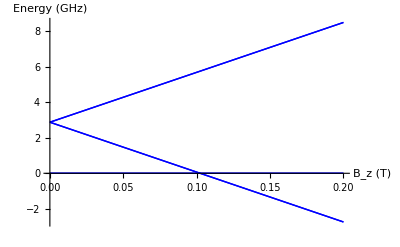

```mathematica
Plot[Evaluate[10^-9 Eigenvalues[H0MAT+UMAT/.parameters]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","Energy (GHz)"},PlotStyle->{{Thick,Blue}}]
```

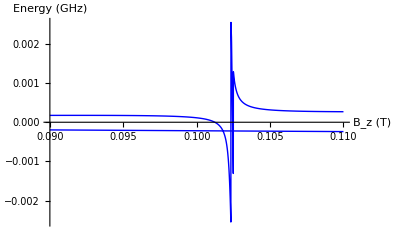

```mathematica
Plot[Evaluate[10^-9 Eigenvalues[H0MAT+UMAT/.parameters]][[5;;6]],{Subscript[B, z],0.09,0.11},AxesLabel->{"B_z (T)","Energy (GHz)"},PlotStyle->{{Thick,Blue}},PlotRange->All]
```

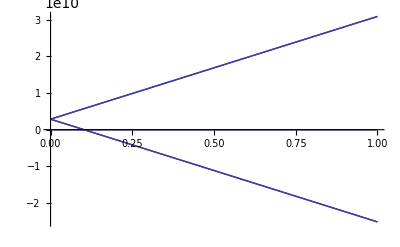

```mathematica
Plot[Eigenvalues[H0MAT+UMAT/.parameters],{Subscript[B, z],0,1}]
```

```mathematica
blocks={{1,2},{3,4},{5,6}};
nb=Length[Flatten[blocks]];
NB=Length[blocks];
```

```mathematica
LöMAT=Table[0,{i,NB},{j,NB}];
Do[LöMAT[[i,i]]=Take[H0MAT,blocks[[i]],blocks[[i]]],{i,NB}];
LöMAT=ArrayFlatten[LöMAT];
```

```mathematica
Do[Do[LöMAT[[m,mp]]=LöMAT[[m,mp]]+1/2 Sum[UMAT[[m,l]]UMAT[[l,mp]](1/(H00MAT[[m,m]]-H00MAT[[l,l]])+1/(H00MAT[[mp,mp]]-H00MAT[[l,l]])),{l,Flatten[Delete[blocks,i]]}],{m,blocks[[i]]},{mp,blocks[[i]]}],
{i,NB}]
```

```mathematica
(*  not really convenient: /.{Δ->Γ+Subscript[B, z] Subscript[μ, e]-Subscript[B, z] Subscript[μ, n]}
```

```mathematica
Do[Print[Take[LöMAT,blocks[[i]],blocks[[i]]]//MF],{i,NB}]
```

(Δ+A_para/2-B_z μ_e-(B_z μ_n)/2 | 0
0 | Δ-A_para/2-B_z μ_e+(B_z μ_n)/2+A_perp^2/(2 (Δ-B_z μ_e+B_z μ_n)))

(-1/2 B_z μ_n+A_perp^2/(2 (-Δ+B_z μ_e-B_z μ_n)) | 0
0 | (B_z μ_n)/2+A_perp^2/(2 (-Δ-B_z μ_e+B_z μ_n)))

(Δ-A_para/2+B_z μ_e-(B_z μ_n)/2+A_perp^2/(2 (Δ+B_z μ_e-B_z μ_n)) | 0
0 | Δ+A_para/2+B_z μ_e+(B_z μ_n)/2)

```mathematica
(* neglect B-field in denominators ~ Δ *)
(*
LöMAT=Normal[Series[LöMAT/.Δ->(1/invΔ),{invΔ,0,1}]];
LöMAT=LöMAT/.invΔ->1/Δ;
```

```mathematica
(* evaluate mistake when ignoring coupling between Subscript[m, s]=0 and Subscript[m, s]=-1 *)
(* LöMAT[[4,4]]=LöMAT[[4,4]]+Subscript[A, perp]^2/(4 Δ);
```

```mathematica
Do[Print[Take[LöMAT,blocks[[i]],blocks[[i]]]//MF],{i,NB}]
```

(Δ+A_para/2-B_z μ_e-(B_z μ_n)/2 | 0
0 | Δ-A_para/2-B_z μ_e+(B_z μ_n)/2+A_perp^2/(2 (Δ-B_z μ_e+B_z μ_n)))

(-1/2 B_z μ_n+A_perp^2/(2 (-Δ+B_z μ_e-B_z μ_n)) | 0
0 | (B_z μ_n)/2+A_perp^2/(2 (-Δ-B_z μ_e+B_z μ_n)))

(Δ-A_para/2+B_z μ_e-(B_z μ_n)/2+A_perp^2/(2 (Δ+B_z μ_e-B_z μ_n)) | 0
0 | Δ+A_para/2+B_z μ_e+(B_z μ_n)/2)

#### Plot energy levels

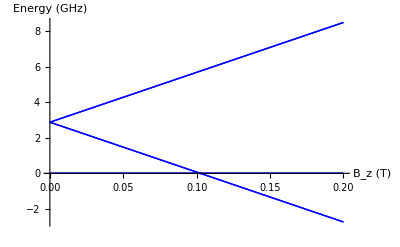

```mathematica
Plot[Evaluate[Table[LöMAT[[m,m]]/10^9/.parameters,{m,nb}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","Energy (GHz)"},PlotStyle->{{Thick,Blue}}]
```

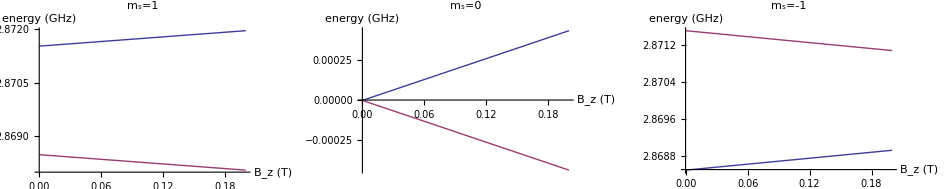

```mathematica
LöMATnoZ=LöMAT/.{Subscript[B, z] Subscript[μ, e]->0};
{Table[Plot[Evaluate[Table[LöMATnoZ[[m,m]]/10^9/.parameters,{m,blocks[[i]]}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","energy (GHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]}//GraphicsGrid
```

#### continue with diagonal blocks

```mathematica
bh=Table[0,{i,NB}];
Do[bh[[i]]=Take[LöMAT,blocks[[i]],blocks[[i]]],{i,NB}]
```

```mathematica
(*Do[Print[bh[[i]]//MF],{i,NB}]
```

```mathematica
heff=Table[{Subscript[Heff, x], Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0]},{i,NB}];
Do[
heff[[i]]=heff[[i]]/.Solve[bh[[i]]==Subscript[Heff, 0] σ0+Subscript[Heff, z] σz/2+Subscript[Heff, x] σx/2+ Subscript[Heff, y] σy/2,{Subscript[Heff, x],Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0]}][[1]]
,{i,NB}];
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n))+2 B_z μ_n (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | (A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(4 (Δ+B_z (-μ_e+μ_n)))
0 | 0 | -(B_z ((-Δ^2+B_z^2 (μ_e-μ_n)^2) μ_n+A_perp^2 (-μ_e+μ_n)))/(-Δ^2+B_z^2 (μ_e-μ_n)^2) | -(Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2))
0 | 0 | -A_para+A_perp^2/(2 (Δ+B_z (μ_e-μ_n)))-B_z μ_n | Δ+B_z μ_e+A_perp^2/(4 (Δ+B_z (μ_e-μ_n))))

```mathematica
heff/.Subscript[B, z]->0//MF
```

(0 | 0 | -(-2 Δ A_para+A_perp^2)/(2 Δ) | (4 Δ^2+A_perp^2)/(4 Δ)
0 | 0 | 0 | -A_perp^2/(2 Δ)
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+A_perp^2/(4 Δ))

#### rotating frame

```mathematica
heff//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n))+2 B_z μ_n (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | (A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(4 (Δ+B_z (-μ_e+μ_n)))
0 | 0 | -(B_z ((-Δ^2+B_z^2 (μ_e-μ_n)^2) μ_n+A_perp^2 (-μ_e+μ_n)))/(-Δ^2+B_z^2 (μ_e-μ_n)^2) | -(Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2))
0 | 0 | -A_para+A_perp^2/(2 (Δ+B_z (μ_e-μ_n)))-B_z μ_n | Δ+B_z μ_e+A_perp^2/(4 (Δ+B_z (μ_e-μ_n))))

•  constant term

```mathematica
heff[[All,4]]=heff[[All,4]]-ConstantArray[heff[[2,4]],3];
heff//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n))+2 B_z μ_n (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | (Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2))+(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(4 (Δ+B_z (-μ_e+μ_n)))
0 | 0 | -(B_z ((-Δ^2+B_z^2 (μ_e-μ_n)^2) μ_n+A_perp^2 (-μ_e+μ_n)))/(-Δ^2+B_z^2 (μ_e-μ_n)^2) | 0
0 | 0 | -A_para+A_perp^2/(2 (Δ+B_z (μ_e-μ_n)))-B_z μ_n | Δ+B_z μ_e+A_perp^2/(4 (Δ+B_z (μ_e-μ_n)))+(Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2)))

•  I_z term

```mathematica
heff[[All,3]]=heff[[All,3]]-ConstantArray[heff[[2,3]],3];
heff//MF
```

(0 | 0 | (B_z ((-Δ^2+B_z^2 (μ_e-μ_n)^2) μ_n+A_perp^2 (-μ_e+μ_n)))/(-Δ^2+B_z^2 (μ_e-μ_n)^2)-(A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n))+2 B_z μ_n (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | (Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2))+(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(4 (Δ+B_z (-μ_e+μ_n)))
0 | 0 | 0 | 0
0 | 0 | -A_para+A_perp^2/(2 (Δ+B_z (μ_e-μ_n)))-B_z μ_n+(B_z ((-Δ^2+B_z^2 (μ_e-μ_n)^2) μ_n+A_perp^2 (-μ_e+μ_n)))/(-Δ^2+B_z^2 (μ_e-μ_n)^2) | Δ+B_z μ_e+A_perp^2/(4 (Δ+B_z (μ_e-μ_n)))+(Δ A_perp^2)/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2)))

```mathematica
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(2 (Δ+B_z (μ_e-μ_n))) | 1/4 ((2 Δ A_perp^2)/(Δ^2-B_z^2 (μ_e-μ_n)^2)+(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(Δ+B_z (-μ_e+μ_n)))
0 | 0 | 0 | 0
0 | 0 | (A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | Δ+B_z μ_e+1/4 A_perp^2 (1/(Δ+B_z (μ_e-μ_n))+(2 Δ)/(Δ^2-B_z^2 (μ_e-μ_n)^2)))

•  S_z term

```mathematica
Solve[a +heff[[1,4]]==heff[[1,3]]/2,a][[1]]
```

{a→-(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(4 (Δ+B_z (μ_e-μ_n)))+1/4 (-(2 Δ A_perp^2)/(Δ^2-B_z^2 (μ_e-μ_n)^2)-(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(Δ+B_z (-μ_e+μ_n)))}

```mathematica
(*Simplify[a/.%92/.Subscript[B, z]->0,Δ>0]
```

A_para/2-(Δ^2+A_perp^2)/Δ

```mathematica
heff[[All,4]]=heff[[All,4]]+Sz.ConstantArray[a/.%,3];
heff//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(2 (Δ+B_z (μ_e-μ_n))) | -(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(4 (Δ+B_z (μ_e-μ_n)))+1/4 (-(2 Δ A_perp^2)/(Δ^2-B_z^2 (μ_e-μ_n)^2)-(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(Δ+B_z (-μ_e+μ_n)))+1/4 ((2 Δ A_perp^2)/(Δ^2-B_z^2 (μ_e-μ_n)^2)+(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(Δ+B_z (-μ_e+μ_n)))
0 | 0 | 0 | 0
0 | 0 | (A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | Δ+B_z μ_e+1/4 A_perp^2 (1/(Δ+B_z (μ_e-μ_n))+(2 Δ)/(Δ^2-B_z^2 (μ_e-μ_n)^2))+(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(4 (Δ+B_z (μ_e-μ_n)))+1/4 ((2 Δ A_perp^2)/(Δ^2-B_z^2 (μ_e-μ_n)^2)+(A_perp^2+4 (Δ-B_z μ_e) (Δ+B_z (-μ_e+μ_n)))/(Δ+B_z (-μ_e+μ_n))))

```mathematica
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | -(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(2 (Δ+B_z (μ_e-μ_n))) | -(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(4 (Δ+B_z (μ_e-μ_n)))
0 | 0 | 0 | 0
0 | 0 | (A_perp^2-2 A_para (Δ+B_z (-μ_e+μ_n)))/(2 (Δ+B_z (-μ_e+μ_n))) | (8 Δ (Δ^2-B_z^2 (μ_e-μ_n)^2)-2 A_para (Δ^2-B_z^2 (μ_e-μ_n)^2)+A_perp^2 (7 Δ+B_z (-μ_e+μ_n)))/(4 (Δ^2-B_z^2 (μ_e-μ_n)^2)))

```mathematica
Subscript[A, net]=Simplify[heff[[1,4]]+heff[[1,3]]/2]
```

-(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(2 (Δ+B_z (μ_e-μ_n)))

A_net=A_para-A_perp^2/(2Γ)

•  apart from a sign error, this agrees with Nemoto2014

```mathematica
Do[Print["m_s=",Sz[[i,i]],":     ",Simplify[σz/2 heff[[i,3]]+σ0 heff[[i,4]]]//MF],{i,NB}];
```

m_s=1:     (-(A_perp^2-2 A_para (Δ+B_z (μ_e-μ_n)))/(2 (Δ+B_z (μ_e-μ_n))) | 0
0 | 0)

m_s=0:     (0 | 0
0 | 0)

m_s=-1:     ((2 Δ (Δ^2+A_perp^2-B_z^2 (μ_e-μ_n)^2)+A_para (-Δ^2+B_z^2 (μ_e-μ_n)^2))/(Δ^2-B_z^2 (μ_e-μ_n)^2) | 0
0 | (4 Δ (Δ^2-B_z^2 (μ_e-μ_n)^2)+A_perp^2 (3 Δ+B_z (-μ_e+μ_n)))/(2 (Δ^2-B_z^2 (μ_e-μ_n)^2)))

#### without rotating frame

•  the B=0 term: 
S_z(α_zx Ij_x+α_zy Ij_y+α_zz Ij_z)

```mathematica
(heff/.{Subscript[B, x]->0,Subscript[B, y]->0,Subscript[B, z]->0}//MF)
```

(0 | 0 | -(-2 Δ A_para+A_perp^2)/(2 Δ) | -(-2 Δ A_para+A_perp^2)/(4 Δ)
0 | 0 | 0 | 0
0 | 0 | (-2 Δ A_para+A_perp^2)/(2 Δ) | (8 Δ^3-2 Δ^2 A_para+7 Δ A_perp^2)/(4 Δ^2))

•  now with constant energy shift

```mathematica
(Simplify[heff/.{Subscript[B, x]->0,Subscript[B, y]->0,Subscript[B, z]->0}]//MF)
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | -(-2 Δ A_para+A_perp^2)/(4 Δ)
0 | 0 | 0 | 0
0 | 0 | -A_para+A_perp^2/(2 Δ) | 2 Δ-A_para/2+(7 A_perp^2)/(4 Δ))

Therefore, 
•  for m_s=+1 or -1 the nucleus feels the hfi as an additional B_z-field   δB =m_s/μ_n(A_para-A_perp^2/(2 Δ))
•  and the m_s=+_-1 levels are pushed away from m_s=0 level by (3 A_perp^2)/(4 Δ)

```mathematica
geff=Table[0,{i,NB},{j,3}];
Do[
geff[[i,j]]=D[heff[[i,1;;3]],BvecFull[[j]]]
,{i,NB},{j,3}];
Do[Print["-μ_ng(m_s=",Sz[[i,i]],")=-μ_n𝕀_3+",Simplify[geff[[i]]+Subscript[μ, n]({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}),Δ>0]//MF],{i,NB}]
```

-μ_ng(m_s=1)=-μ_n𝕀_3+(0 | 0 | 0
0 | 0 | 0
0 | 0 | (A_perp^2 (μ_e-μ_n)+2 (Δ+B_z (μ_e-μ_n))^2 μ_n)/(2 (Δ+B_z (μ_e-μ_n))^2))

-μ_ng(m_s=0)=-μ_n𝕀_3+(0 | 0 | 0
0 | 0 | 0
0 | 0 | μ_n)

-μ_ng(m_s=-1)=-μ_n𝕀_3+(0 | 0 | 0
0 | 0 | 0
0 | 0 | (A_perp^2 (μ_e-μ_n)+2 μ_n (Δ+B_z (-μ_e+μ_n))^2)/(2 (Δ+B_z (-μ_e+μ_n))^2))

•  first two rows (x&y) are not meaningful because we didn't allow for perpendicular B components
•  combined

g^eff(m_s)=𝕀_3

### ^14N

```mathematica
parameters={Δ->2.87 10^9,Subscript[μ, e]->28.031 10^9,Q->-4.946 10^6,Subscript[μ, n]->3.0766 10^6,Subscript[A, para]->-2.165 10^6,Subscript[A, perp]->-2.7 10^6};
```

```mathematica
H00MAT=Δ KroneckerProduct[Sz^2,S0]-Subscript[μ, e] Subscript[B, z] KroneckerProduct[Sz,S0];
H0MAT=Δ KroneckerProduct[Sz^2,S0]-Subscript[μ, e] Subscript[B, z] KroneckerProduct[Sz,S0]+Q KroneckerProduct[S0,Sz^2]-Subscript[μ, n] Subscript[B, z] KroneckerProduct[S0,Sz]+Subscript[α, zz] KroneckerProduct[Sz,Sz]/.{Subscript[α, zz]->Subscript[A, para]};
UMAT=Subscript[α, xx] KroneckerProduct[Sx,Sx]+Subscript[α, yy] KroneckerProduct[Sy,Sy]/.{Subscript[α, xx]->Subscript[A, perp],Subscript[α, yy]->Subscript[A, perp]};
```

```mathematica
H0MAT//MF
```

(Q+Δ+A_para-B_z μ_e-B_z μ_n | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δ-B_z μ_e | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Q+Δ-A_para-B_z μ_e+B_z μ_n | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Q-B_z μ_n | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Q+B_z μ_n | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Q+Δ-A_para+B_z μ_e-B_z μ_n | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ+B_z μ_e | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Q+Δ+A_para+B_z μ_e+B_z μ_n)

```mathematica
UMAT//MF
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | A_perp | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | A_perp | 0 | 0 | 0 | 0
0 | A_perp | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | A_perp | 0 | 0 | 0 | A_perp | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | A_perp | 0
0 | 0 | 0 | 0 | A_perp | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | A_perp | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
blocks=Table[3i+j,{i,0,2},{j,1,3}];
nb=Length[Flatten[blocks]];
NB=Length[blocks];
```

```mathematica
LöMAT=Table[0,{i,NB},{j,NB}];
Do[LöMAT[[i,i]]=Take[H0MAT,{blocks[[i,1]],blocks[[i,-1]]},{blocks[[i,1]],blocks[[i,-1]]}],{i,NB}];
LöMAT=ArrayFlatten[LöMAT];
```

```mathematica
Refine[LöMAT==H0MAT]
```

True

```mathematica
Do[Do[LöMAT[[m,mp]]=LöMAT[[m,mp]]+1/2 Sum[UMAT[[m,l]]UMAT[[l,mp]](1/(H00MAT[[m,m]]-H00MAT[[l,l]])+1/(H00MAT[[mp,mp]]-H00MAT[[l,l]])),{l,Flatten[Delete[blocks,i]]}],{m,blocks[[i]]},{mp,blocks[[i]]}],
{i,NB}]
```

```mathematica
(*  not really convenient: /.{Δ->Γ+Subscript[B, z] Subscript[μ, e]-Subscript[B, z] Subscript[μ, n]}
```

```mathematica
Do[Print[Take[LöMAT,{blocks[[i,1]],blocks[[i,-1]]},{blocks[[i,1]],blocks[[i,-1]]}]//MF],{i,NB}]
```

(Q+Δ+A_para-B_z μ_e-B_z μ_n | 0 | 0
0 | Δ-B_z μ_e+A_perp^2/(Δ-B_z μ_e) | 0
0 | 0 | Q+Δ-A_para-B_z μ_e+A_perp^2/(Δ-B_z μ_e)+B_z μ_n)

(Q+A_perp^2/(-Δ+B_z μ_e)-B_z μ_n | 0 | 0
0 | 1/2 ((2 A_perp^2)/(-Δ-B_z μ_e)+(2 A_perp^2)/(-Δ+B_z μ_e)) | 0
0 | 0 | Q+A_perp^2/(-Δ-B_z μ_e)+B_z μ_n)

(Q+Δ-A_para+B_z μ_e+A_perp^2/(Δ+B_z μ_e)-B_z μ_n | 0 | 0
0 | Δ+B_z μ_e+A_perp^2/(Δ+B_z μ_e) | 0
0 | 0 | Q+Δ+A_para+B_z μ_e+B_z μ_n)

```mathematica
(* neglect B-field in denominators ~ Δ *)

LöMAT=Normal[Series[LöMAT/.Δ->(1/invΔ),{invΔ,0,1}]];LöMAT
LöMAT=LöMAT/.invΔ->1/Δ;
```

{{1/invΔ+Q+A_para-B_z μ_e-B_z μ_n,0,0,0,0,0,0,0,0},{0,1/invΔ+invΔ A_perp^2-B_z μ_e,0,0,0,0,0,0,0},{0,0,1/invΔ+Q-A_para+invΔ A_perp^2-B_z μ_e+B_z μ_n,0,0,0,0,0,0},{0,0,0,Q-invΔ A_perp^2-B_z μ_n,0,0,0,0,0},{0,0,0,0,-2 invΔ A_perp^2,0,0,0,0},{0,0,0,0,0,Q-invΔ A_perp^2+B_z μ_n,0,0,0},{0,0,0,0,0,0,1/invΔ+Q-A_para+invΔ A_perp^2+B_z μ_e-B_z μ_n,0,0},{0,0,0,0,0,0,0,1/invΔ+invΔ A_perp^2+B_z μ_e,0},{0,0,0,0,0,0,0,0,1/invΔ+Q+A_para+B_z μ_e+B_z μ_n}}

```mathematica
bh=Table[0,{i,NB}];
Do[bh[[i]]=Take[LöMAT,{blocks[[i,1]],blocks[[i,-1]]},{blocks[[i,1]],blocks[[i,-1]]}],{i,NB}]
```

```mathematica
Do[Print[bh[[i]]//MF],{i,NB}]
```

(Q+Δ+A_para-B_z μ_e-B_z μ_n | 0 | 0
0 | Δ+A_perp^2/Δ-B_z μ_e | 0
0 | 0 | Q+Δ-A_para+A_perp^2/Δ-B_z μ_e+B_z μ_n)

(Q-A_perp^2/Δ-B_z μ_n | 0 | 0
0 | -(2 A_perp^2)/Δ | 0
0 | 0 | Q-A_perp^2/Δ+B_z μ_n)

(Q+Δ-A_para+A_perp^2/Δ+B_z μ_e-B_z μ_n | 0 | 0
0 | Δ+A_perp^2/Δ+B_z μ_e | 0
0 | 0 | Q+Δ+A_para+B_z μ_e+B_z μ_n)

The following stuff differs from the spin-1/2 nuclei above, since there are three equations, so one needs a third term ~Sz^2 (in addition to S0, Sz)

```mathematica
heff=Table[{Subscript[Heff, x], Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0],Subscript[Heff, z2]},{i,NB}];
Do[
heff[[i]]=heff[[i]]/.Solve[(bh[[i]]/.Q->0)==Subscript[Heff, 0] S0+Subscript[Heff, z] Sz+Subscript[Heff, x] Sx+ Subscript[Heff, y] Sy+Subscript[Heff, z2] Sz^2,{Subscript[Heff, x],Subscript[Heff, y],Subscript[Heff, z],Subscript[Heff, 0],Subscript[Heff, z2]}][[1]]
,{i,NB}];
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ)-B_z μ_n | Δ+A_perp^2/Δ-B_z μ_e | -A_perp^2/(2 Δ)
0 | 0 | -B_z μ_n | -(2 A_perp^2)/Δ | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ)-B_z μ_n | Δ+A_perp^2/Δ+B_z μ_e | -A_perp^2/(2 Δ))

#### Plot energy levels

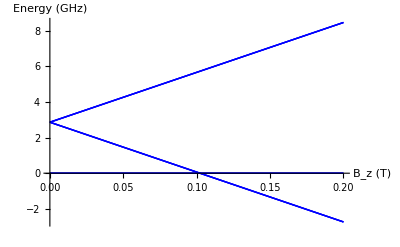

```mathematica
Plot[Evaluate[Table[LöMAT[[m,m]]/10^9/.parameters,{m,nb}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","Energy (GHz)"},PlotStyle->{{Thick,Blue}}]
```

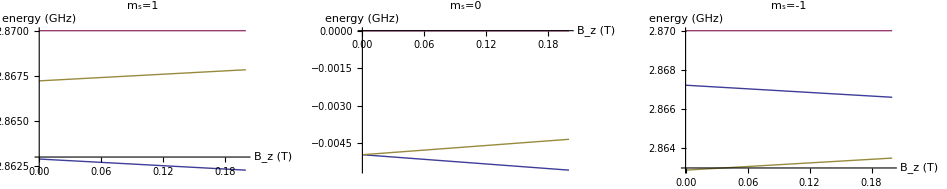

```mathematica
LöMATnoZ=LöMAT/.{Subscript[B, z] Subscript[μ, e]->0};
{Table[Plot[Evaluate[Table[LöMATnoZ[[m,m]]/10^9/.parameters,{m,blocks[[i]]}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","energy (GHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]}//GraphicsGrid
```

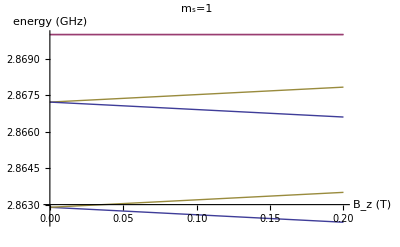

```mathematica
LöMATnoZ=LöMAT/.{Subscript[B, z] Subscript[μ, e]->0};
Show[Table[Plot[Evaluate[Table[LöMATnoZ[[m,m]]/10^9/.parameters,{m,blocks[[i]]}]],{Subscript[B, z],0,0.2},AxesLabel->{"B_z (T)","energy (GHz)"},PlotStyle->Thick,PlotLabel->Row[{"m_s=",Sz[[i,i]]}]],{i,NB}]]
```

#### rotating frame (not evaluated)

```mathematica
heff//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ)-B_z μ_n | Δ+A_perp^2/Δ-B_z μ_e | -A_perp^2/(2 Δ)
0 | 0 | -B_z μ_n | -(2 A_perp^2)/Δ | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ)-B_z μ_n | Δ+A_perp^2/Δ+B_z μ_e | -A_perp^2/(2 Δ))

•  constant term

```mathematica
heff[[All,4]]=heff[[All,4]]-ConstantArray[heff[[2,4]],3];
heff//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ)-B_z μ_n | Δ+(3 A_perp^2)/Δ-B_z μ_e | -A_perp^2/(2 Δ)
0 | 0 | -B_z μ_n | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ)-B_z μ_n | Δ+(3 A_perp^2)/Δ+B_z μ_e | -A_perp^2/(2 Δ))

•  I_z term

```mathematica
heff[[All,3]]=heff[[All,3]]-ConstantArray[heff[[2,3]],3];
heff//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ-B_z μ_e | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ+B_z μ_e | -A_perp^2/(2 Δ))

```mathematica
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ-B_z μ_e | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ+B_z μ_e | -A_perp^2/(2 Δ))

•  S_z term

```mathematica
Solve[a +heff[[1,4]]==heff[[1,3]]/2,a][[1]]
```

{a→(-4 Δ^2+2 Δ A_para-13 A_perp^2+4 Δ B_z μ_e)/(4 Δ)}

```mathematica
heff[[1,4]]=heff[[1,4]]+a/.%;
heff//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ-B_z μ_e+(-4 Δ^2+2 Δ A_para-13 A_perp^2+4 Δ B_z μ_e)/(4 Δ) | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ+B_z μ_e | -A_perp^2/(2 Δ))

```mathematica
(heff=Simplify[heff,Δ>0])//MF
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | A_para/2-A_perp^2/(4 Δ) | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ+B_z μ_e | -A_perp^2/(2 Δ))

```mathematica
Subscript[A, net]=Simplify[heff[[1,4]]+heff[[1,3]]/2]
```

A_para-A_perp^2/(2 Δ)

```mathematica
Do[Print["m_s=",Sz[[i,i]],":     ",Simplify[σz/2 heff[[i,3]]+σ0 heff[[i,4]]]//MF],{i,NB}];
```

m_s=1:     (A_para-A_perp^2/(2 Δ) | 0
0 | 0)

m_s=0:     (0 | 0
0 | 0)

m_s=-1:     (Δ-A_para/2+(13 A_perp^2)/(4 Δ)+B_z μ_e | 0
0 | Δ+A_para/2+(11 A_perp^2)/(4 Δ)+B_z μ_e)

#### without rotating frame

•  the B=0 term: 
S_z(α_zx Ij_x+α_zy Ij_y+α_zz Ij_z)

```mathematica
(heff/.{Subscript[B, x]->0,Subscript[B, y]->0,Subscript[B, z]->0}//MF)
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | A_para/2-A_perp^2/(4 Δ) | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ | -A_perp^2/(2 Δ))

•  now with constant energy shift

```mathematica
(Simplify[heff/.{Subscript[B, x]->0,Subscript[B, y]->0,Subscript[B, z]->0}]//MF)
```

(0 | 0 | A_para-A_perp^2/(2 Δ) | A_para/2-A_perp^2/(4 Δ) | -A_perp^2/(2 Δ)
0 | 0 | 0 | 0 | A_perp^2/Δ
0 | 0 | -A_para+A_perp^2/(2 Δ) | Δ+(3 A_perp^2)/Δ | -A_perp^2/(2 Δ))

Therefore, 
•  for m_s=+1 or -1 the nucleus feels the hfi as an additional B_z-field   δB =m_s/μ_n(A_para-A_perp^2/(4 Δ))
•  and the m_s=+_-1 levels are pushed away from m_s=0 level by (3 A_perp^2)/(8 Δ)

```mathematica
geff=Table[0,{i,NB},{j,3}];
Do[
geff[[i,j]]=D[heff[[i,1;;3]],BvecFull[[j]]]
,{i,NB},{j,3}];
Do[Print["-μ_ng(m_s=",Sz[[i,i]],")=",Simplify[geff[[i]],Δ>0]//MF],{i,NB}]
```

Part::partd: Part specification BvecFull ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification BvecFull ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification BvecFull ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

-μ_ng(m_s=1)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

-μ_ng(m_s=0)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

-μ_ng(m_s=-1)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

•  first two rows (x&y) are not meaningful because we didn't allow for perpendicular B components
•  combined

g^eff(m_s)=𝕀_3

•  ^14 N-^13 C: only dipole-dipole interaction, but this is too weak [Dutt2007]

## n-n interactions

•  ^14N-^13C: only dipole-dipole interaction, but this is too weak [Dutt2007]
•  ^13C-^13C: direct dipole-dipole interaction + electron-mediated interaction

## References

[Childress2006] Childress et al., Science , Vol. 314, p. 281 (2006)
[Nemoto2014] Nemoto et al., Phys. Rev. X , Vol. 4 , p. 031022 (2006)
[Dutt2007] Science , Vol. 316, p. 1312
[Zaiser2019] Zaiser, PhD thesis